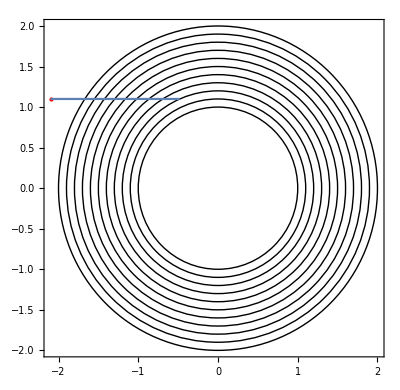

```mathematica
Clear["Global`*"];

(* Assumptions:
 shells are located around the origin
light rays never bend more than 90 degrees
*)

(* shells are composed of the following: the circle graphic, the circle equation, the circle radius, the n value *)
(* more will be added to shells as we get into physical properties *)
Shell[r_,n_]:={Circle[{0,0},r],x^2+y^2==r^2,r,n}; 
Ray[point_,θ_]:=y-point[[2]]==Tan[θ] (x-point[[1]]);
NormalAngle[point_]:=ArcTan[point[[1]],point[[2]]];
IsPointReal[point_]:=(x/.point)∈Reals&&( y/.point)∈Reals;

SnellsLaw[θin_,nin_,nout_]:=ArcSin[Sin[θin]nin/nout];

(* make an atmosphere with linearly-spaced shells specified by minimum, maximum, and step size of radius *)
MakeAtmosphere[min_,max_,step_]:=Module[{r,center,nMax,nStep,n},
atmosphere={};

(* TODO - filling in dummy n values for now- probably make a function to pull from actually state variables to calculate n values later *)
nMax = 1.0;
nStep = (nMax-1.)/((max-min)/step);
n = 1.;
Do[
{
n+=nStep,
atmosphere =Append[atmosphere,Shell[r,n]]
},
{r,min,max,step}
];
]

(* make the graphics objects *)
MakeAtmosphereGraphic[atm_]:=Table[Graphics[{atmosphere[[i,1]]}],{i,1,Length[atm]}];
MakeIntersectionsPointsGraphic[intersections_]:=Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];

FindNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},
x0 = rayPosition[[1]];
y0 = rayPosition[[2]];
m=Tan[rayAngle];
t1 = (-x0-m y0 + √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2 = (-x0-m y0 - √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);

(* return only real positive time values *)
tList=Select[{t1,t2},(#∈Reals&&#>0)&]
]

(* function that identifies where the light currently is in relation to shells *)
LocateLightRay[position_,atm_]:=Module[{shellRadii,posRadius},
{
shellRadii = atm[[All,3]];
posRadius = √(position[[1]]^2+position[[2]]^2);
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Last[shellRadii]== posRadius,
rayLocation = "on outer shell",

(* on some non-outer shell *)
MemberQ[shellRadii,posRadius],
rayLocation = "on",

(* between shells (only possible remaining case) *)
!MemberQ[shellRadii,posRadius],
rayLocation = "between"
]
}
]

(* updates the light position based on current position, direction, and shells *)
(* TODO - need to handle the case where it's at the end of the last atmosphere layer *)
MoveLightRay[ray_,rayOrigin_,rayAngle_,atm_]:=Module[{direction,checkShellNum,closestIntersect,sol,location,currentShell,tList,intersect,t},
position = rayOrigin;
posRadius = √(position[[1]]^2+position[[2]]^2);

location  = LocateLightRay[position,atm];

Which[
(* only need to check the outermost shell *)
location == {"outside"},
t = Min[FindNextShellIntersection[Last[atm][[3]],position,rayAngle]],

(* only need to check the innermost shell *)
location == {"inside"},
t = Min[FindNextShellIntersection[First[atm][[3]],position,rayAngle]],

(* only need to check the second-outermost shell unless it's a one-shell atmosphere *)
location == {"on outer shell"},
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
t = Min[FindNextShellIntersection[atm[[-2,3]],position,rayAngle]],

(* else if it's a single-shell atmosphere *)
t = Min[FindNextShellIntersection[atm[[1,3]],position,rayAngle]]
]
},

(* need to check the shells before and after the one it's on *)
location == {"on"},
{
currentShell = Position[atm[[All,3]],posRadius],

t = Min[Join[
FindNextShellIntersection[atm[[currentShell[[1,1]]+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[currentShell[[1,1]]-1,3]],position,rayAngle]
]
]
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == {"between"},
{
Print["atm between"],
currentShell =Length[atm],
While[atm[[currentShell,3]] > posRadius,
currentShell-=1; 
],
tList = Join[
FindNextShellIntersection[atm[[currentShell,3]],position,rayAngle],
FindNextShellIntersection[atm[[currentShell+1,3]],position,rayAngle]
],
t= Min[tList]
}
];

(* stuff to be done regardless of ray location case *)
{
(* non-intersection case *)
If[t==Infinity,
t = 1, (* just set t to some small value (probably adjust to fit window size later *)
{}
],

intersect = {t+position[[1]],Tan[rayAngle ] t + position[[2]]},
position = intersect;
(* TODO - also output the shell that it is currently interacting with *)
}
]

(* get the n1 angle needed for Snell's Law given the ray entry and the shell *)
Refract[position_,angle_]:=Module[{θ1},
Which[
(* hitting shell from outside in *)
position[[1]]<0,
(* TODO - this should be okay now- though the other conditions still need to be tested *)
Return[NormalAngle[position]-π+SnellsLaw[(π-NormalAngle[position]+angle),1.,1.]],

(* hitting shell from inside out *)
position[[1]]>0,
Return[π-NormalAngle[position]-angle],

(* hitting the top of bottom of a shell- could be either outside-in or inside-out *)
position [[1]]== 0,
{
Which[
angle≠ 0,
θ1 = Return[π/2-Abs[angle]],

angle == 0,

Print["non-intersection case"]
(*TODO non-intersecting grazing case *)

]
}
]
]

(*run the program starting here *)
origin = {-2.1,1.1}; (* origin needs to be specified by doubles rather than ints *)
angle = 0;
lightRay = Ray[origin,angle];

intersectionPoints = {origin};

MakeAtmosphere[1,2,0.1];
 (*TODO - hack - shouldn't need the [[2]]*)
AppendTo[intersectionPoints,MoveLightRay[lightRay,origin,angle,atmosphere][[2]]];

(* snell's law stuff starts here *)
Do[
{
angle=Refract[position,angle];
AppendTo[intersectionPoints,MoveLightRay[Ray[position,angle],position,angle,atmosphere][[2]]]
},
{i,1,8}
]

(* TODO- something's with my angles... probably the angle out calculation *)
(* graphics stuff starts here *)
Show[MakeAtmosphereGraphic[atmosphere],Graphics[{Red,Point[origin]}],ListLinePlot[intersectionPoints],Frame-> True]
(*
LineGraphic=ListLinePlot[{origin,intersect}];

Show[MakeAtmosphereGraphic[atmosphere],MakeIntersectionsPointsGraphic[intersect],LineGraphic,Frame->True]
*)
```